### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/Examples/ExamplesParameters.m"];
g[x]
```

Log[x]

```mathematica
Get["/Users/ribeirrd/eclipse-workspace/MFGraphs/MFGraphs/MFGraphs.m"];
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Currents→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,4,S1},{1,2,3,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
MFGEquations=DataToEquations[Data/.{I1->3,U1->(*at vertex 3*)1,U2->(*at vertex 4*)0(*, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1*),S1->(*S124*)2,S2->(*S123*)S2,S3->0,S4->0,S5->0,S6->0}];//Timing
Print["current: ", MFGEquations["jvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["transition: ", MFGEquations["jtvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
Print["value: ", MFGEquations["uvars"]/.MFGEquations["criticalreduced1"][[2]]//KeySort]
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: After NewReduce, the system is:
jt383==0&&j373==0&&S2==2&&u391==2&&u390==2&&u389==7&&jt380==2&&j367==2
and the rules are:
<|j370→3,u398→1,u399→0,j365→3,j366→3+j373-jt380-jt383,j368→3+j373-jt380-jt383,j369→j367,j371→0,j372→j367-jt380-jt383,j374→j367-jt380-jt383,j375→j373,j376→0,jt377→0,jt378→3,jt379→3-jt380,jt381→-jt383,jt382→j367-jt380,jt384→j373-jt383,jt385→3+j373-jt380-jt383,jt386→j367-jt380-jt383,jt387→j367,jt388→j373,u392→1,u393→0,u395→-3+u389,u396→-3+j367-j373+u390,u397→-j367+j373+u391,u400→u389,u394→u389|>

DataToEquations: It took 0.113501 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.14067,Null}

current: <|{1,1->2}→0,{1,en362->1}→3,{2,1->2}→3,{2,2->3}→0,{2,2->4}→0,{3,2->3}→1,{3,3->ex363}→0,{4,2->4}→2,{4,4->ex364}→0,{en362,en362->1}→0,{ex363,3->ex363}→1,{ex364,4->ex364}→2|>

transition: <|{1,1->2,en362->1}→0,{1,en362->1,1->2}→3,{2,1->2,2->3}→1,{2,1->2,2->4}→2,{2,2->3,1->2}→0,{2,2->3,2->4}→0,{2,2->4,1->2}→0,{2,2->4,2->3}→0,{3,2->3,3->ex363}→1,{3,3->ex363,2->3}→0,{4,2->4,4->ex364}→2,{4,4->ex364,2->4}→0|>

value: <|{1,1->2}→7,{1,en362->1}→7,{2,1->2}→4,{2,2->3}→2,{2,2->4}→2,{3,2->3}→1,{3,3->ex363}→1,{4,2->4}→0,{4,4->ex364}→0,{en362,en362->1}→7,{ex363,3->ex363}→1,{ex364,4->ex364}→0|>

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: The system is:
NonNegative[2-j289]&&NonNegative[j289]&&NonNegative[2-j289]&&NonNegative[j289]&&NonNegative[2-jt302]&&NonNegative[jt302]&&NonNegative[-j289+jt302]&&NonNegative[j289-jt302]&&NonNegative[j289-jt302]&&NonNegative[-j289+jt302]&&NonNegative[2-j289]&&NonNegative[j289]&&NonNegative[2-u311+u312]&&NonNegative[2-u311+u313]&&NonNegative[-2+u311-u312]&&NonNegative[-u312+u313]&&NonNegative[-2+u311-u313]&&NonNegative[u312-u313]&&NonNegative[7-j289-u312]&&NonNegative[1+j289-u313]&&(2-jt302==0||-j289+jt302==0)&&(jt302==0||j289-jt302==0)&&(j289-jt302==0||-j289+jt302==0)&&(2-jt302==0||2-u311+u312==0)&&(jt302==0||2-u311+u313==0)&&(-j289+jt302==0||-2+u311-u312==0)&&(j289-jt302==0||-u312+u313==0)&&(j289-jt302==0||-2+u311-u313==0)&&(-j289+jt302==0||u312-u313==0)&&(2-j289==0||7-j289-u312==0)&&(j289==0||1+j289-u313==0)
and the rules are:
<|j292→2,u320→5,u321→1,j287→2,j288→2-j289,j290→2-j289,j291→j289,j293→0,j294→0,j295→0,j296→0,j297→0,j298→0,jt299→0,jt300→2,jt301→2-jt302,jt303→-j289+jt302,jt304→j289-jt302,jt305→j289-jt302,jt306→-j289+jt302,jt307→2-j289,jt308→0,jt309→j289,jt310→0,u314→5,u315→1,u317→-2+u311,u318→-2+j289+u312,u319→-j289+u313,u322→u311,u316→u311|>

DataToEquations: It took 0.03768 seconds to reduce with NewReduce!

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.055495,Null}

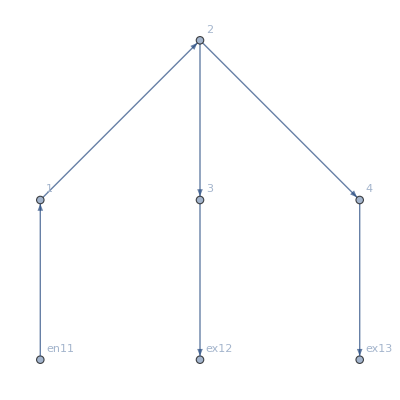

<|{1,1->2}→u506,{1,en479->1}→u506,{2,1->2}→-1+u506,{2,2->3}→u507,{2,2->4}→u508,{3,2->3}→-1+j484+u507,{3,3->ex480}→5,{4,2->4}→-j484+u508,{4,4->ex481}→1,{en479,en479->1}→u506,{ex480,3->ex480}→5,{ex481,4->ex481}→1|>

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]](*//KeySort*)
```

<|j253→2,u281→5,u282→1,j248→2,j249→0,j251→0,j252→2,j254→0,j255→0,j256→0,j257→0,j258→0,j259→0,jt260→0,jt261→2,jt262→0,jt264→0,jt265→0,jt266→0,jt267→0,jt268→0,jt269→0,jt270→2,jt271→0,u275→5,u276→1,u278→3,u279→3,u280→1,u283→5,u277→5,j250→2,jt263→2,u272→5,u273→3,u274→3|>

```mathematica
DataToEquations
```

#### Non-linear case

```mathematica
alpha = 0;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10]//KeySort
```

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,
SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 1.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```